```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-up-xi1-pi-noD.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgf=Interpolation[Flatten[Hdgu,1]];
Herf=Interpolation[Flatten[Heru,1]];
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-dleta-pi-xi1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;

dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;


dHerf=Interpolation[Flatten[dHeru,1]];


dEerf=Interpolation[Flatten[dEeru,1]];

Dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-D-xi1-pi.wdx"];

DHeru=Query[1,2]@Dgpdu;
DHdau=Query[1,3]@Dgpdu;

DEeru=Query[2,2]@Dgpdu;
DEdau=Query[2,3]@Dgpdu;

DHerf=Interpolation[Flatten[DHeru,1]];
dDgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-dleta-D-pi-xi1.wdx"];

dDHeru=Query[1,2]@dDgpdu;


dDEeru=Query[2,2]@dDgpdu;


dDHerf=Interpolation[Flatten[dDHeru,1]];
```

```mathematica
(*先把上面的结果组合起来*)
```

```mathematica
Hdgall[x_,t_]:=Hdgf[x,t];
Herall[x_,t_]:=Herf[x,t]+dHerf[x,t]+DHerf[x,t]+dDHerf[x,t];
```

```mathematica
(*u quark*)
```

```mathematica
(*npi+,只需要乘上系数*)
Coep1=(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
(*pi+的u贡献，分段但就是总的*)
p1Hdg[x_,t_]=Coep1*Hdgall[x,t];
p1Her[x_,t_]=Coep1*Herall[x,t];
```

```mathematica
(*pi0,先系数再多一个来自input的1/2，求和之后整体反转*)
ap0=(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
(*pi0的u，之后要和反转的求和*)
p0Hdg[x_,t_]=ap0*Hdgall[x,t];
p0Her[x_,t_]=ap0*Herall[x,t];


(*反转*)
p0Hdg0[x_,t_]=-p0Hdg[-x,t];
p0Her0[x_,t_]=-p0Her[-x,t];

(*求和,只有erbl要加起来，以及画图也是分段那其实只要算erbl*)
p0Herre[x_,t_]=p0Her[x,t]+p0Her0[x,t];

(*图的总结果，就是对粒子求和*)
Hdgzall[x_,t_]=p1Hdg[x,t]+p0Hdg[x,t];
Hdgfall[x_,t_]=p0Hdg0[x,t];
Herallwhole[x_,t_]=p1Her[x,t]+p0Herre[x,t];
```

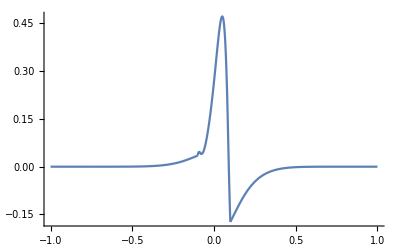

```mathematica
Show[Plot[-I*Hdgzall[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Hdgfall[x,-1],{x,-1,-0.1},PlotRange->All],Plot[-I*Herallwhole[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
Herallwhole[0.05,-1]
```

0.+0.471945 ⅈ

```mathematica
(*d quark*)
```

```mathematica
(*npi+,dbar=u，所以之后再对dbar反转得到d*)
(*pi+的dbar贡献就是u，反转*)
p1Hdgd[x_,t_]=-p1Hdg[-x,t];
p1Herd[x_,t_]=-p1Her[-x,t];


(*pi0,u=d，所以直接套用u的形式*)
(*图的总结果，就是对粒子求和*)
Hdgzalld[x_,t_]=p0Hdg[x,t];
Hdgfalld[x_,t_]=p1Hdgd[x,t]+p0Hdg0[x,t];
Herallwholed[x_,t_]=p1Herd[x,t]+p0Herre[x,t];
```

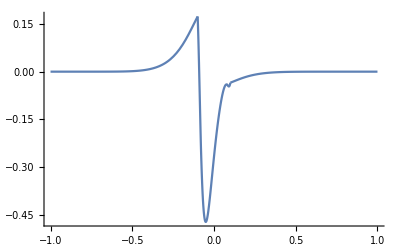

```mathematica
Show[Plot[-I*Hdgzalld[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Hdgfalld[x,-1],{x,-1,-0.1},PlotRange->All],Plot[-I*Herallwholed[x,-1],{x,-0.1,0.1},PlotRange->All]]
```